# Chapter 8: Advanced Techniques and Wolfram Language Integration

This chapter demonstrates sophisticated workflows that combine the server-side processing power of Google Earth Engine with the analytical, visualization, and machine learning capabilities of the Wolfram Language. Each section builds on the fundamentals covered in earlier chapters to show what becomes possible when these two platforms work together.

Prerequisite: Authenticate per Section 1.3 and load the paclet with Needs["GoogleEarthEngineClient`"].

## 8.1 Machine Learning with GEE Data

The Wolfram Language provides a complete machine learning stack through Classify, Predict, FindClusters, and related functions. By extracting spectral data from GEE and feeding it into these built-in learners, you can build land cover classifiers, biomass predictors, and unsupervised clustering models without leaving a single notebook.

## Supervised Classification: Land Cover from Sentinel-2

The general workflow is: define training points with known labels, extract multi-band spectral values at those points using GEEGetSamples, train a classifier, and evaluate its performance. For an application of this workflow to crop-type classification specifically, see Section 5.3.2.

Step 1: Define training locations and labels.

Each training point is a GeoPosition with a known land cover class. In practice you would derive these from field surveys, existing land cover maps, or careful visual interpretation.

```mathematica
(* Training points: {GeoPosition, class label} *)
trainingPoints = {
  (* Water *)
 {GeoPosition[{45.44, 12.34}], "Water"},
 {GeoPosition[{45.43, 12.35}], "Water"},
{GeoPosition[{45.45, 12.33}], "Water"},
{GeoPosition[{34.21559,-83.97755}], "Water"},
{GeoPosition[{32.17563,-80.57786}], "Water"},
  (* Forest *)
{GeoPosition[{46.05, 11.12}], "Forest"},
{GeoPosition[{46.06, 11.13}], "Forest"},
{GeoPosition[{46.07, 11.11}], "Forest"},
{GeoPosition[{46.07, 11.11}], "Forest"},
{GeoPosition[{36.03586, -81.73847}], "Forest"},
{GeoPosition[{47.75114, -83.68864}], "Forest"},
  (* Cropland *)
{GeoPosition[{45.10, 11.80}], "Crop"},
{GeoPosition[{45.11, 11.81}], "Crop"},
{GeoPosition[{45.12, 11.79}], "Crop"},
{GeoPosition[{39.66382, -90.03569}], "Crop"},
{GeoPosition[{-34.27094, -60.01783}], "Crop"},
  (* Urban *)
{GeoPosition[{45.46, 9.19}], "Urban"},
{GeoPosition[{45.47, 9.18}], "Urban"},
{GeoPosition[{45.48, 9.20}], "Urban"},
{GeoPosition[{-34.75792, -58.32966}], "Urban"},
{GeoPosition[{-33.92940,18.41720}], "Urban"},
  (* Bare soil *)
{GeoPosition[{44.80, 11.50}], "Bare"},
{GeoPosition[{44.81, 11.51}], "Bare"},
{GeoPosition[{44.81, 11.51}], "Bare"},
{GeoPosition[{-24.45847, 15.17605}], "Bare"},
{GeoPosition[{39.10261, 84.42859}], "Bare"}
};
```

Note: This minimal training set (5 points per class, 25 total) is for illustration only. Production classifications require 50+ samples per class with stratified sampling.

Step 2: Build a cloud-free Sentinel-2 composite and extract spectral values.

The pipeline selects bands B2 through B12 (visible, red edge, NIR, SWIR) because these carry the spectral information that distinguishes land cover types.

```mathematica
sentinel2 =
  GEECollection["COPERNICUS/S2_SR_HARMONIZED"] //
    GEEFilterDate["2024-06-01", "2024-09-01"] //
    GEEFilterProperty["CLOUDY_PIXEL_PERCENTAGE", "LessThan", 10] //
    GEESelectBands[{"B2", "B3", "B4", "B5", "B6", "B7", "B8", "B8A",
      "B11", "B12"}] //
    GEEMedian;

(* Extract band values at all training points *)
samples = GEEGetSamples[
  trainingPoints[[All, 1]],
  sentinel2,
  "Bands" ->(#<>"_median")&/@ {"B2", "B3", "B4", "B5", "B6", "B7", "B8", "B8A",
    "B11", "B12"}
];
```

Step 3: Build training data and train a classifier.

The Classify function accepts training data as {feature -> label, ...} rules. Each feature vector is the list of band values for that pixel.

```mathematica
(* Pair each sample's spectral values with its label *)
trainingData = MapThread[
  #1["Values"] -> #2 &,
  {samples, trainingPoints[[All, 2]]}
];

(* Train with Random Forest *)
classifier = Classify[trainingData, Method -> "RandomForest"]
```

ClassifierFunction[…]

Step 4: Evaluate model performance.

ClassifierMeasurements provides accuracy, confusion matrix, F1 scores, and many other diagnostics.

0.807692

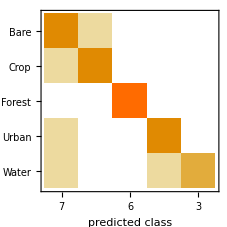

<|Bare→0.666667,Crop→0.8,Forest→1.,Urban→0.8,Water→0.75|>

```mathematica
(* Note: Evaluating on the training set overstates accuracy. For rigorous
   evaluation, split data into training and test sets or use cross-validation. *)
cm = ClassifierMeasurements[classifier, trainingData];

(* Overall accuracy *)
cm["Accuracy"]

(* Confusion matrix -- shows where classes are being mixed *)
cm["ConfusionMatrixPlot"]

(* Per-class F1 score *)
cm["F1Score"]
```

Step 5: Apply the classifier to new locations.

```mathematica
newPoints = {
  GeoPosition[{45.50, 12.00}],
  GeoPosition[{46.10, 11.20}],
  GeoPosition[{45.00, 11.90}]
};

newSamples = GEEGetSamples[newPoints, sentinel2,
  "Bands" -> (#<>"_median")&/@{"B2", "B3", "B4", "B5", "B6", "B7", "B8", "B8A",
    "B11", "B12"}];

predictions = classifier /@ (newSamples[[All, "Values"]])
(* e.g. {"Water", "Forest", "Crop"} *)
```

{Bare,Forest,Bare}

## Unsupervised Clustering

When you do not have labeled training data, FindClusters can discover natural groupings in spectral space. This is useful for exploratory analysis to understand what surface types exist in a scene.

```mathematica
(* Sample a grid of points across a region *)
gridPoints = Flatten[
  Table[
    GeoPosition[{lat, lon}],
    {lat, 45.0, 45.5, 0.05},
    {lon, 11.0, 11.5, 0.05}
  ]
];

gridSamples = GEEGetSamples[gridPoints, sentinel2,
  "Bands" -> (#<>"_median")&/@{"B2", "B3", "B4", "B5", "B6", "B7", "B8", "B11", "B12"}];

spectralVectors = gridSamples[[All, "Values"]];

(* Cluster into 5 groups *)
clusters = FindClusters[spectralVectors, 5, Method -> "KMeans"];
```

Visualize the spectral space with dimensionality reduction.

Reducing to 2 or 3 dimensions helps you see whether the clusters are well separated, which indicates distinct surface types.

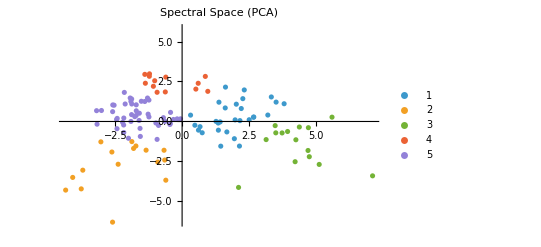

```mathematica
reduced = DimensionReduce[spectralVectors, 2,
  Method -> "PrincipalComponentsAnalysis"];

(* Assign cluster labels to each point *)
clusterLabels = FindClusters[
  spectralVectors -> Range[Length[spectralVectors]], 5
];
(* clusterLabels is a list of groups of indices -- flatten to per-point labels *)
pointLabels = ConstantArray[0, Length[spectralVectors]];
Do[
  (pointLabels[[#]] = k) & /@ clusterLabels[[k]],
  {k, Length[clusterLabels]}
];

(* Note: This is a conceptual sketch. FindClusters returns groups of indices,
   not per-point labels. The loop above converts groups to per-point labels
   for plotting. *)

ListPlot[
  Table[
    Pick[reduced, pointLabels, k],
    {k, Length[clusterLabels]}
  ],
  PlotLabel -> "Spectral Space (PCA)",
  FrameLabel -> {"PC1", "PC2"},
  PlotLegends -> Range[Length[clusterLabels]]
]
```

## Regression: Predicting Biomass from Spectral Indices

For continuous target variables such as biomass, crop yield, or soil moisture, use Predict instead of Classify.

```mathematica
(* Training data: spectral indices paired with field-measured biomass (kg/m^2) *)
biomassTraining = {
     (* {NDVI, EVI, NDWI} -> biomass *)
  {2.080762759394279,0.6593601895734598,-0.6332361516034986}->283,{0.932815241915267,0.45639641849625906,-0.5277920741121976}->8,{2.683884988298228,0.8882434301521438,-0.7864433394399372}->184
};

biomassPredictor = Predict[biomassTraining, Method -> "RandomForest"]

(* Predict biomass for new spectral measurements *)
biomassPredictor[{0.65, 0.30, 0.17}]
```

PredictorFunction[…]

101.47

To extract the spectral indices from GEE for the prediction input:

```mathematica
ndviImage =
  sentinel2 //
    GEENormalizedDifference[{"B8_median", "B4_median"}] //
    GEERename[{"NDVI"}];

eviImage =
  sentinel2 //
    GEEExpression[
      "2.5 * ((NIR - RED) / (NIR + 6 * RED - 7.5 * BLUE + 1))",
      <|"NIR" -> "B8_median", "RED" -> "B4_median", "BLUE" -> "B2_median"|>
    ] //
    GEERename[{"EVI"}];

ndwiImage =
  sentinel2 //
    GEENormalizedDifference[{"B3_median", "B8_median"}] //
    GEERename[{"NDWI"}];

indexStack =
  ndviImage //
    GEEAddBands[eviImage] //
    GEEAddBands[ndwiImage];

(*Create a dense sampling grid within a field*)
fieldPoints=Flatten[Table[GeoPosition[{lat,lon}],{lat,32.92,32.97,0.005},{lon,-84.1,-84.02,0.005}],1];

fieldSamples = GEEGetSamples[fieldPoints, indexStack,
  "Bands" -> {"NDVI", "EVI", "NDWI"}];
```

```mathematica
predictedBiomass = biomassPredictor /@ (fieldSamples[[All, "Values"]])
```

{208.373,208.373,208.373,208.373,208.373,101.47,201.549,208.373,219.745,208.373,208.373,208.373,208.373,208.373,219.745,208.373,208.373,208.373,201.549,208.373,208.373,208.373,208.373,208.373,208.373,208.373,208.373,208.373,208.373,208.373,208.373,208.373,208.373,208.373,208.373,201.549,201.549,201.549,208.373,208.373,208.373,208.373,208.373,178.804,208.373,201.549,219.745,208.373,208.373,208.373,208.373,208.373,208.373,208.373,208.373,208.373,208.373,208.373,208.373,208.373,208.373,201.549,208.373,208.373,208.373,208.373,208.373,101.47,208.373,208.373,208.373,233.392,190.177,208.373,208.373,208.373,208.373,208.373,208.373,208.373,208.373,208.373,208.373,208.373,208.373,208.373,201.549,208.373,208.373,208.373,208.373,201.549,101.47,208.373,187.902,208.373,208.373,219.745,208.373,101.47,208.373,208.373,167.431,208.373,101.47,101.47,190.177,219.745,201.549,208.373,208.373,187.902,201.549,208.373,208.373,208.373,101.47,208.373,190.177,208.373,208.373,201.549,101.47,208.373,201.549,201.549,101.47,219.745,219.745,201.549,208.373,201.549,201.549,208.373,208.373,219.745,101.47,208.373,208.373,208.373,208.373,208.373,208.373,201.549,208.373,208.373,208.373,201.549,101.47,101.47,201.549,178.804,208.373,101.47,208.373,208.373,208.373,208.373,208.373,208.373,208.373,208.373,208.373,192.451,208.373,208.373,135.588,208.373,201.549,201.549,101.47,101.47,208.373,208.373,208.373,208.373,208.373,208.373,208.373,208.373,208.373,208.373,208.373,101.47,101.47,208.373,201.549}

```mathematica
GeoHistogram[Thread[Rule[fieldSamples[[All,"Position"]],predictedBiomass]],GeoBackground->"Satellite",ColorFunction->(Which[#>200,DarkGreen,#>150,LightGreen,#>100,Yellow,True,White]&),ColorFunctionScaling->False,PlotLegends->Automatic]
```

-Graphics-

## 8.2 Time Series Analysis

You have seen the monthly-loop pattern in earlier chapters. This section focuses on what to do after you have the time series -- trend detection, anomaly flagging, and forecasting.

## Building Multi-Year Time Series

The general pattern is to iterate over time windows, compute a regional statistic for each window using GEECompute with GEEReduceRegion, and assemble the results into a TimeSeries object.

```mathematica
(* Define region of interest: a forest polygon *)
forestPolygon = GEEPolygon[{
  {-72.5, -13.0}, {-72.3, -13.0}, {-72.3, -12.8},
  {-72.5, -12.8}, {-72.5, -13.0}
}];

(* Generate monthly date ranges over 5 years *)
dateRanges = Table[
  {
    DateString[DateObject[{year, month, 1}], {"Year", "-", "Month", "-", "Day"}],
    DateString[
      DatePlus[DateObject[{year, month, 1}], {1, "Month"}],
      {"Year", "-", "Month", "-", "Day"}
    ]
  },
  {year, 2019, 2023},
  {month, 1, 12}
] // Flatten[#, 1] &;

(* Extract mean NDVI for each month *)
ndviTimeSeries = Table[
  Module[{pipeline, result},
    pipeline =
      GEECollection["MODIS/061/MOD13A2"] //
        GEEFilterDate[dates[[1]], dates[[2]]] //
        GEESelectBands[{"NDVI"}] //
        GEEMean //
        GEEMultiply[0.0001] //  (* Apply MODIS scale factor *)
        GEEReduceRegion[forestPolygon, "mean", 1000];
    result = GEECompute[pipeline];
    {DateObject[dates[[1]]], result}
  ],
  {dates, dateRanges}
];

(* Build a TimeSeries object *)
ndviTS = TimeSeries[
  ndviTimeSeries[[All, 2]],
  {ndviTimeSeries[[All, 1]]}
];

DateListPlot[ndviTS,
  PlotLabel -> "Monthly Mean NDVI (2019-2023)",
  FrameLabel -> {"Date", "NDVI"},
  Filling -> Axis
]
```

$Aborted

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

TimeSeries::invstrct: The data TimeSeries[Symbol[],{Symbol[]},{ResamplingMethod→{Interpolation,InterpolationOrder→1}}] is not a structurally valid TemporalData object.

DateListPlot::ldata: TimeSeries[Symbol[],{Symbol[]}] is not a valid dataset or list of datasets.

DateListPlot[TimeSeries[Symbol[],{Symbol[]}],PlotLabel→Monthly Mean NDVI (2019-2023),FrameLabel→{Date,NDVI},Filling→Axis]

```mathematica
result
```

result

```mathematica
ndviTS//Normal
```

{{Tue 1 Jan 2019 00:00:00GMT-4,Missing[KeyAbsent,NDVI]},{Fri 1 Feb 2019 00:00:00GMT-4,Missing[KeyAbsent,NDVI]},{Fri 1 Mar 2019 00:00:00GMT-4,Missing[KeyAbsent,NDVI]},{Mon 1 Apr 2019 00:00:00GMT-4,Missing[KeyAbsent,NDVI]},{Wed 1 May 2019 00:00:00GMT-4,Missing[KeyAbsent,NDVI]},{Sat 1 Jun 2019 00:00:00GMT-4,Missing[KeyAbsent,NDVI]},{Mon 1 Jul 2019 00:00:00GMT-4,Missing[KeyAbsent,NDVI]},{Thu 1 Aug 2019 00:00:00GMT-4,Missing[KeyAbsent,NDVI]},{Sun 1 Sep 2019 00:00:00GMT-4,Missing[KeyAbsent,NDVI]},{Tue 1 Oct 2019 00:00:00GMT-4,Missing[KeyAbsent,NDVI]},{Fri 1 Nov 2019 00:00:00GMT-4,Missing[KeyAbsent,NDVI]},{Sun 1 Dec 2019 00:00:00GMT-4,Missing[KeyAbsent,NDVI]},{Wed 1 Jan 2020 00:00:00GMT-4,Missing[KeyAbsent,NDVI]},{Sat 1 Feb 2020 00:00:00GMT-4,Missing[KeyAbsent,NDVI]},{Sun 1 Mar 2020 00:00:00GMT-4,Missing[KeyAbsent,NDVI]},{Wed 1 Apr 2020 00:00:00GMT-4,Missing[KeyAbsent,NDVI]},{Fri 1 May 2020 00:00:00GMT-4,Missing[KeyAbsent,NDVI]},{Mon 1 Jun 2020 00:00:00GMT-4,Missing[KeyAbsent,NDVI]},{Wed 1 Jul 2020 00:00:00GMT-4,Missing[KeyAbsent,NDVI]},{Sat 1 Aug 2020 00:00:00GMT-4,Missing[KeyAbsent,NDVI]},{Tue 1 Sep 2020 00:00:00GMT-4,Missing[KeyAbsent,NDVI]},{Thu 1 Oct 2020 00:00:00GMT-4,Missing[KeyAbsent,NDVI]},{Sun 1 Nov 2020 00:00:00GMT-4,Missing[KeyAbsent,NDVI]},{Tue 1 Dec 2020 00:00:00GMT-4,Missing[KeyAbsent,NDVI]},{Fri 1 Jan 2021 00:00:00GMT-4,Missing[KeyAbsent,NDVI]},{Mon 1 Feb 2021 00:00:00GMT-4,Missing[KeyAbsent,NDVI]},{Mon 1 Mar 2021 00:00:00GMT-4,Missing[KeyAbsent,NDVI]},{Thu 1 Apr 2021 00:00:00GMT-4,Missing[KeyAbsent,NDVI]},{Sat 1 May 2021 00:00:00GMT-4,Missing[KeyAbsent,NDVI]},{Tue 1 Jun 2021 00:00:00GMT-4,Missing[KeyAbsent,NDVI]},{Thu 1 Jul 2021 00:00:00GMT-4,Missing[KeyAbsent,NDVI]},{Sun 1 Aug 2021 00:00:00GMT-4,Missing[KeyAbsent,NDVI]},{Wed 1 Sep 2021 00:00:00GMT-4,Missing[KeyAbsent,NDVI]},{Fri 1 Oct 2021 00:00:00GMT-4,Missing[KeyAbsent,NDVI]},{Mon 1 Nov 2021 00:00:00GMT-4,Missing[KeyAbsent,NDVI]},{Wed 1 Dec 2021 00:00:00GMT-4,Missing[KeyAbsent,NDVI]},{Sat 1 Jan 2022 00:00:00GMT-4,Missing[KeyAbsent,NDVI]},{Tue 1 Feb 2022 00:00:00GMT-4,Missing[KeyAbsent,NDVI]},{Tue 1 Mar 2022 00:00:00GMT-4,Missing[KeyAbsent,NDVI]},{Fri 1 Apr 2022 00:00:00GMT-4,Missing[KeyAbsent,NDVI]},{Sun 1 May 2022 00:00:00GMT-4,Missing[KeyAbsent,NDVI]},{Wed 1 Jun 2022 00:00:00GMT-4,Missing[KeyAbsent,NDVI]},{Fri 1 Jul 2022 00:00:00GMT-4,Missing[KeyAbsent,NDVI]},{Mon 1 Aug 2022 00:00:00GMT-4,Missing[KeyAbsent,NDVI]},{Thu 1 Sep 2022 00:00:00GMT-4,Missing[KeyAbsent,NDVI]},{Sat 1 Oct 2022 00:00:00GMT-4,Missing[KeyAbsent,NDVI]},{Tue 1 Nov 2022 00:00:00GMT-4,Missing[KeyAbsent,NDVI]},{Thu 1 Dec 2022 00:00:00GMT-4,Missing[KeyAbsent,NDVI]},{Sun 1 Jan 2023 00:00:00GMT-4,Missing[KeyAbsent,NDVI]},{Wed 1 Feb 2023 00:00:00GMT-4,Missing[KeyAbsent,NDVI]},{Wed 1 Mar 2023 00:00:00GMT-4,Missing[KeyAbsent,NDVI]},{Sat 1 Apr 2023 00:00:00GMT-4,Missing[KeyAbsent,NDVI]},{Mon 1 May 2023 00:00:00GMT-4,Missing[KeyAbsent,NDVI]},{Thu 1 Jun 2023 00:00:00GMT-4,Missing[KeyAbsent,NDVI]},{Sat 1 Jul 2023 00:00:00GMT-4,Missing[KeyAbsent,NDVI]},{Tue 1 Aug 2023 00:00:00GMT-4,Missing[KeyAbsent,NDVI]},{Fri 1 Sep 2023 00:00:00GMT-4,Missing[KeyAbsent,NDVI]},{Sun 1 Oct 2023 00:00:00GMT-4,Missing[KeyAbsent,NDVI]},{Wed 1 Nov 2023 00:00:00GMT-4,Missing[KeyAbsent,NDVI]},{Fri 1 Dec 2023 00:00:00GMT-4,Missing[KeyAbsent,NDVI]}}

## Trend Detection

A linear fit to the time series reveals whether vegetation is greening (positive slope) or browning (negative slope) over the study period. For non-linear dynamics, FindFit can model logistic growth, exponential decay, or other functional forms.

```mathematica
(* Convert dates to numeric values for fitting *)
numericDates = AbsoluteTime /@ ndviTimeSeries[[All, 1]];
ndviValues = ndviTimeSeries[[All, 2]];

(* Linear trend *)
lm = LinearModelFit[
  Transpose[{numericDates, ndviValues}],
  x, x
];

(* Slope tells you the rate of change *)
slope = lm["BestFitParameters"][[2]];
Print["NDVI trend: ", slope * (365.25 * 86400), " per year"]

(* Nonlinear fit: logistic recovery model *)
logisticModel = FindFit[
  Transpose[{numericDates - Min[numericDates], ndviValues}],
  k / (1 + a * Exp[-r * t]),
  {k, a, r}, t
];

Show[
  ListPlot[Transpose[{numericDates, ndviValues}]],
  Plot[lm[x], {x, Min[numericDates], Max[numericDates]}, PlotStyle -> Red],
  PlotLabel -> "NDVI Trend Detection"
]
```

## Seasonal Decomposition

Fourier analysis separates the time series into its constituent frequencies, letting you isolate the annual cycle from multi-year trends and short-term noise.

```mathematica
(* Fourier transform of NDVI series *)
ft = Fourier[ndviValues];

(* Periodogram reveals dominant frequencies *)
Periodogram[ndviValues,
  PlotLabel -> "NDVI Frequency Spectrum",
  SampleRate -> 12  (* monthly data = 12 samples/year *)
]

(* Isolate seasonal component using bandpass filter *)
(* Pass frequencies near 1 cycle/year *)
seasonalComponent = BandpassFilter[ndviValues, {0.8/12, 1.2/12}];

(* Trend: low-pass filter *)
trendComponent = LowpassFilter[ndviValues, 0.5/12];

(* Residual = original - trend - seasonal *)
residualComponent = ndviValues - trendComponent - seasonalComponent;

GraphicsRow[{
  ListLinePlot[trendComponent, PlotLabel -> "Trend"],
  ListLinePlot[seasonalComponent, PlotLabel -> "Seasonal"],
  ListLinePlot[residualComponent, PlotLabel -> "Residual"]
}, ImageSize -> Large]
```

## Anomaly Detection

Anomalies are months where observed NDVI deviates significantly from the long-term climatological mean for that calendar month. This approach can flag drought, flooding, or land use change events.

```mathematica
(* Group values by calendar month *)
monthlyGroups = GroupBy[
  ndviTimeSeries,
  DateValue[#[[1]], "Month"] &,
  #[[All, 2]] &
];

(* Compute climatological mean and standard deviation per month *)
climatology = Association @ Table[
  month -> <|
    "Mean" -> Mean[monthlyGroups[month]],
    "StdDev" -> StandardDeviation[monthlyGroups[month]]
  |>,
  {month, Keys[monthlyGroups]}
];

(* Flag anomalies: months deviating more than 2 sigma *)
anomalies = Select[ndviTimeSeries,
  Module[{month, val, clim},
    month = DateValue[#[[1]], "Month"];
    val = #[[2]];
    clim = climatology[month];
    Abs[val - clim["Mean"]] > 2 * clim["StdDev"]
  ] &
];

Print["Detected ", Length[anomalies], " anomalous months"]
Print["Anomaly dates: ", anomalies[[All, 1]]]
```

## Forecasting

TimeSeriesForecast uses the structure it detects in the historical data (trend, seasonality, autocorrelation) to project forward.

```mathematica
(* Forecast the next 12 months *)
forecast = TimeSeriesForecast[ndviTS, {12}];

DateListPlot[{ndviTS, forecast},
  PlotLabel -> "NDVI Forecast (12 months)",
  PlotLegends -> {"Historical", "Forecast"},
  FrameLabel -> {"Date", "NDVI"}
]
```

## 8.3 Image Processing Pipeline

The paclet delivers GEE raster data as Wolfram Image objects. Once client-side, the full power of the Wolfram Language image processing stack is available for enhancement, segmentation, edge detection, and change analysis.

## Enhancement for Publication-Quality Output

Raw satellite imagery often needs contrast adjustment and color balancing before it is suitable for publication or reports.

```mathematica
(* Fetch a Sentinel-2 true-color image *)
rawImage = GEEComputePixels[
  {12.4, 41.8, 12.6, 42.0},
  GEECollection["COPERNICUS/S2_SR_HARMONIZED"] //
    GEEFilterDate["2024-06-01", "2024-08-31"] //
    GEEFilterProperty["CLOUDY_PIXEL_PERCENTAGE", "LessThan", 5] //
    GEESelectBands[{"B4", "B3", "B2"}] //
    GEEMedian //
    GEEVisualize[<|"min" -> 0, "max" -> 3000|>],
  "ImageSize" -> 1024
];

(* Enhance *)
enhanced =
  rawImage //
    ImageAdjust[#, {0.1, 0.2}] & //   (* Contrast and brightness *)
    Sharpen[#, 2] & //                 (* Edge enhancement *)
    ColorBalance;                       (* White balance correction *)

(* Match a reference histogram for consistent styling *)
referenceImage = Import["reference_scene.png"];
matched = HistogramTransform[enhanced, referenceImage];

GraphicsRow[{rawImage, enhanced, matched},
  ImageSize -> Large,
  PlotLabel -> {"Raw", "Enhanced", "Histogram Matched"}
]
```

## Segmentation: Counting Crop Fields

Thresholding an NDVI image and analyzing connected components lets you count and measure individual features such as crop fields or water bodies.

```mathematica
(* Compute NDVI image *)
ndviRaster = GEEComputePixels[
  {11.0, 44.8, 11.4, 45.0},
  GEECollection["COPERNICUS/S2_SR_HARMONIZED"] //
    GEEFilterDate["2024-07-01", "2024-08-31"] //
    GEEFilterProperty["CLOUDY_PIXEL_PERCENTAGE", "LessThan", 10] //
    GEEMedian //
    GEENormalizedDifference[{"B8", "B4"}] //
    GEEVisualize[<|"min" -> -0.2, "max" -> 0.9,
      "palette" -> {"brown", "yellow", "green", "darkgreen"}|>],
  "ImageSize" -> 512
];

(* Threshold to isolate high-NDVI vegetation *)
binary = Binarize[ndviRaster, 0.5];

(* Identify connected components *)
components = MorphologicalComponents[binary];
nFields = Max[components];

(* Measure each component *)
measurements = ComponentMeasurements[components,
  {"Area", "Centroid", "EquivalentDiskRadius", "Perimeter"}
];

Print["Detected ", nFields, " crop fields"]

(* Filter by minimum area to remove noise *)
significantFields = Select[measurements, #[[2, 1]] > 100 &];
Print["Significant fields (>100 pixels): ", Length[significantFields]]
```

The same segmentation workflow applies to water detection: compute NDWI (GEENormalizedDifference[{"B3", "B8"}]), threshold, and run MorphologicalComponents and ComponentMeasurements to count and measure individual water bodies.

## Edge Detection: Coastline Extraction

EdgeDetect finds boundaries in an image, which is useful for extracting coastlines, field boundaries, or urban edges.

```mathematica
(* NDWI-based water mask for a coastal area *)
coastalNDWI = GEEComputePixels[
  {-5.0, 36.7, -4.8, 36.9},
  GEECollection["COPERNICUS/S2_SR_HARMONIZED"] //
    GEEFilterDate["2024-05-01", "2024-08-31"] //
    GEEFilterProperty["CLOUDY_PIXEL_PERCENTAGE", "LessThan", 10] //
    GEEMedian //
    GEENormalizedDifference[{"B3", "B8"}] //
    GEEVisualize[<|"min" -> -0.5, "max" -> 0.5|>],
  "ImageSize" -> 512
];

coastline = EdgeDetect[Binarize[coastalNDWI, 0.2]];

(* Extract linear features *)
lines = ImageLines[coastline, 0.1, Method -> "Hough"];

Show[coastalNDWI, Graphics[{Red, Thick, Line /@ lines}]]
```

## Change Detection with Image Differencing

Comparing images from two dates reveals changes in land cover, urban growth, deforestation, or flood extent.

```mathematica
(* Before image *)
beforeImage = GEEComputePixels[
  {116.3, 39.8, 116.5, 40.0},
  GEECollection["COPERNICUS/S2_SR_HARMONIZED"] //
    GEEFilterDate["2020-06-01", "2020-08-31"] //
    GEEFilterProperty["CLOUDY_PIXEL_PERCENTAGE", "LessThan", 10] //
    GEEMedian //
    GEENormalizedDifference[{"B8", "B4"}] //
    GEEVisualize[<|"min" -> -0.2, "max" -> 0.8|>],
  "ImageSize" -> 512
];

(* After image *)
afterImage = GEEComputePixels[
  {116.3, 39.8, 116.5, 40.0},
  GEECollection["COPERNICUS/S2_SR_HARMONIZED"] //
    GEEFilterDate["2024-06-01", "2024-08-31"] //
    GEEFilterProperty["CLOUDY_PIXEL_PERCENTAGE", "LessThan", 10] //
    GEEMedian //
    GEENormalizedDifference[{"B8", "B4"}] //
    GEEVisualize[<|"min" -> -0.2, "max" -> 0.8|>],
  "ImageSize" -> 512
];

(* Pixel-wise difference *)
changeImage = ImageDifference[afterImage, beforeImage];

(* Emphasize changes *)
emphasizedChange = changeImage // ImageAdjust // ColorNegate;

GraphicsRow[{beforeImage, afterImage, emphasizedChange},
  PlotLabel -> {"2020", "2024", "Change"}
]
```

## 8.4 Geographic Visualization

The Wolfram Language's geographic visualization functions integrate naturally with GEE data, enabling everything from simple point overlays to interactive multi-panel dashboards.

## GeoGraphics and GEEGeoGraphics

GEEGeoGraphics places Wolfram Language geographic primitives on top of a GEE satellite basemap instead of the default map tiles.

```mathematica
(* Sample points overlaid on a GEE satellite background *)
sampleLocations = {
  GeoPosition[{40.42, -3.70}],
  GeoPosition[{40.45, -3.68}],
  GeoPosition[{40.40, -3.72}]
};

GEEGeoGraphics[
  {Red, PointSize[Large], Point /@ sampleLocations},
  GEECollection["COPERNICUS/S2_SR_HARMONIZED"] //
    GEEFilterDate["2024-06-01", "2024-08-31"] //
    GEEFilterProperty["CLOUDY_PIXEL_PERCENTAGE", "LessThan", 10] //
    GEESelectBands[{"B4", "B3", "B2"}] //
    GEEMedian //
    GEEVisualize[<|"min" -> 0, "max" -> 3000|>],
  GeoRange -> Quantity[15, "Kilometers"],
  GeoCenter -> GeoPosition[{40.42, -3.70}],
  ImageSize -> 600
]
```

For standard basemaps (without GEE imagery), use the built-in GeoGraphics:

```mathematica
GeoGraphics[
  {Red, PointSize[Large], Point /@ sampleLocations,
   EdgeForm[{Thick, Blue}], FaceForm[None],
   Polygon[GeoPosition[{{40.41, -3.71}, {40.43, -3.71},
     {40.43, -3.69}, {40.41, -3.69}}]]
  },
  GeoRange -> Quantity[10, "Kilometers"],
  GeoCenter -> GeoPosition[{40.42, -3.70}]
]
```

## Thematic Mapping: Choropleth and Bubble Charts

GeoRegionValuePlot creates choropleth maps from named geographic entities. This is powerful when combined with GEEReduceRegion or GEEComputeFeatures to extract per-region statistics.

```mathematica
(* Compute mean NDVI per US state *)
states = EntityList[EntityClass["AdministrativeDivision", "USStatesKind"]];

stateNDVI = Table[
  Module[{gb, bbox, pipeline, result},
    gb = GeoBoundingBox[state];
    (* Extract {west, south, east, north} from the bounding box *)
    bbox = {gb[[1, 2]], gb[[1, 1]], gb[[2, 2]], gb[[2, 1]]};
    pipeline =
      GEECollection["MODIS/061/MOD13A2"] //
        GEEFilterDate["2024-06-01", "2024-08-31"] //
        GEESelectBands[{"NDVI"}] //
        GEEMean //
        GEEMultiply[0.0001] //
        GEEReduceRegion[
          GEEGeometry[bbox],
          "mean", 5000
        ];
    result = GEECompute[pipeline];
    state -> result["NDVI"]
  ],
  {state, states}
];

GeoRegionValuePlot[stateNDVI,
  PlotLabel -> "Mean Summer NDVI by US State (2024)",
  ColorFunction -> "GreenBrownTerrain",
  PlotLegends -> Automatic
]
```

GeoBubbleChart displays proportional symbols, useful for showing point-based measurements with magnitude.

```mathematica
(* Bubble chart of NDVI at field sites *)
fieldData = {
  GeoPosition[{38.9, -77.0}] -> 0.65,
  GeoPosition[{34.0, -118.2}] -> 0.32,
  GeoPosition[{41.8, -87.6}] -> 0.48,
  GeoPosition[{29.7, -95.3}] -> 0.55
};

GeoBubbleChart[fieldData,
  PlotLabel -> "Field Site NDVI",
  BubbleSizes -> {0.02, 0.06}
]
```

## Multi-Panel Layouts

Side-by-side comparison is essential for seasonal analysis, before/after studies, and multi-band visualization.

```mathematica
(* Four-season comparison *)
seasons = {
  {"2024-01-01", "2024-03-31", "Winter"},
  {"2024-04-01", "2024-06-30", "Spring"},
  {"2024-07-01", "2024-09-30", "Summer"},
  {"2024-10-01", "2024-12-31", "Fall"}
};

bbox = {-122.5, 37.7, -122.3, 37.9};

seasonImages = Table[
  GEEComputePixels[bbox,
    GEECollection["COPERNICUS/S2_SR_HARMONIZED"] //
      GEEFilterDate[s[[1]], s[[2]]] //
      GEEFilterBounds[bbox] //
      GEEFilterProperty["CLOUDY_PIXEL_PERCENTAGE", "LessThan", 20] //
      GEESelectBands[{"B4", "B3", "B2"}] //
      GEEMedian //
      GEEVisualize[<|"min" -> 0, "max" -> 3000|>],
    "ImageSize" -> 256
  ] -> s[[3]],
  {s, seasons}
];

GraphicsGrid[
  Partition[
    Labeled[#[[1]], #[[2]], Top] & /@ seasonImages,
    2
  ],
  ImageSize -> 800
]
```

## Interactive Exploration

Manipulate lets you build interactive controls that dynamically change GEE query parameters. This is particularly useful during exploratory analysis.

```mathematica
Manipulate[
  GEEComputePixels[
    {-122.5, 37.7, -122.3, 37.9},
    GEECollection["COPERNICUS/S2_SR_HARMONIZED"] //
      GEEFilterDate[
        DateString[startDate, {"Year", "-", "Month", "-", "Day"}],
        DateString[DatePlus[startDate, {3, "Month"}],
          {"Year", "-", "Month", "-", "Day"}]
      ] //
      GEEFilterProperty["CLOUDY_PIXEL_PERCENTAGE", "LessThan", cloudMax] //
      GEESelectBands[{"B4", "B3", "B2"}] //
      GEEMedian //
      GEEVisualize[<|"min" -> 0, "max" -> maxReflectance|>],
    "ImageSize" -> 512
  ],
  {{startDate, DateObject[{2024, 1, 1}], "Start Date"},
    DateObject[{2020, 1, 1}], DateObject[{2024, 10, 1}]},
  {{cloudMax, 15, "Max Cloud %"}, 1, 50, 1},
  {{maxReflectance, 3000, "Max Reflectance"}, 500, 6000, 100}
]
```

For more complex dashboards, DynamicModule provides full control over state management, letting you combine multiple controls (popup menus, sliders, checkboxes) with dynamically updated GEE imagery and plots.

## 8.5 Data Import/Export and Interoperability

Real-world analyses rarely use GEE data in isolation. You typically combine satellite imagery with field measurements, climate model output, census data, or other geospatial layers.

## Importing External Data

CSV tabular data:

```mathematica
(* Field measurements with coordinates *)
fieldData = Import["field_measurements.csv", "Dataset", HeaderLines -> 1];

(* Extract coordinates for GEE sampling *)
fieldPoints = GeoPosition /@ Normal[fieldData[All, {"Latitude", "Longitude"}]];
```

GeoJSON for region definitions:

```mathematica
(* Parse GeoJSON to extract polygon coordinates for GEE *)
geojson = Import["study_area.geojson", "RawJSON"];
coords = geojson["features"][[1]]["geometry"]["coordinates"][[1]];

(* Convert to GEE polygon -- GeoJSON uses {lon, lat} order *)
studyArea = GEEPolygon[coords];

(* Use the polygon to clip a GEE image *)
clippedImage =
  GEECollection["COPERNICUS/S2_SR_HARMONIZED"] //
    GEEFilterDate["2024-06-01", "2024-08-31"] //
    GEEMedian //
    GEESelectBands[{"B4", "B3", "B2"}] //
    GEEClip[studyArea];
```

Other formats: GeoTIFF, NetCDF, and KML all import with a single call:

```mathematica
externalDEM = Import["local_dem.tif", "GeoTIFF"];
tempGrid = Import["climate_model.nc", {"NetCDF", "tas"}];
kmlData = Import["study_sites.kml"];
```

## Exporting Results

Raster images:

```mathematica
(* Save enhanced satellite image *)
Export["enhanced_composite.png", enhanced]

(* High-resolution TIFF *)
Export["analysis_result.tif", ndviRaster]
```

Tabular results:

```mathematica
(* Export sampled data as CSV *)
resultsDataset = Dataset[
  MapThread[
    <|"Lat" -> #1[[1, 1]], "Lon" -> #1[[1, 2]],
      "NDVI" -> #2|> &,
    {fieldPoints, predictedBiomass}
  ]
];

Export["ndvi_results.csv", resultsDataset]
```

GeoJSON for GIS interchange:

```mathematica
(* Build GeoJSON from analysis results *)
features = Table[
  <|
    "type" -> "Feature",
    "geometry" -> <|
      "type" -> "Point",
      "coordinates" -> {pt[[1, 2]], pt[[1, 1]]}  (* lon, lat *)
    |>,
    "properties" -> <|"ndvi" -> val|>
  |>,
  {pt, fieldPoints}, {val, predictedBiomass}
] // Flatten;

geojsonOutput = <|
  "type" -> "FeatureCollection",
  "features" -> features
|>;

Export["output.geojson", geojsonOutput, "RawJSON"]
```

## KML/KMZ for Google Earth

Building KML from GEE query results lets you share findings with collaborators who use Google Earth.

```mathematica
(* Generate KML placemarks from sampled data *)
kmlPlacemarks = StringJoin @@ Table[
  StringTemplate[
    "<Placemark><name>Site `i`</name>\
     <description>NDVI: `val`</description>\
     <Point><coordinates>`lon`,`lat`,0</coordinates></Point>\
     </Placemark>\n"
  ][<|"i" -> i, "val" -> predictedBiomass[[i]],
      "lon" -> fieldPoints[[i, 1, 2]],
      "lat" -> fieldPoints[[i, 1, 1]]|>],
  {i, Length[fieldPoints]}
];

kmlDoc = "<?xml version=\"1.0\"?>\n<kml xmlns=\"http://www.opengis.net/kml/2.2\">\n\
<Document><name>NDVI Samples</name>\n" <> kmlPlacemarks <> "</Document>\n</kml>";

Export["sample_points.kml", kmlDoc, "Text"]
```

## 8.6 Physical Units and Quantities

The Wolfram Language Quantity system ensures unit-aware calculations, eliminating a common source of error when converting between measurement systems. Solar geometry functions add physical context to satellite observations.

## Unit-Aware Area Calculations

GEEArea returns values in square meters. Converting to more practical units is straightforward with Quantity and UnitConvert.

```mathematica
(* Compute the area of a study region *)
regionPoly = GEEPolygon[{
  {-73.0, 4.0}, {-72.5, 4.0}, {-72.5, 4.5},
  {-73.0, 4.5}, {-73.0, 4.0}
}];

areaM2 = GEECompute[GEEArea[regionPoly]];

(* Convert to practical units *)
areaKm2 = UnitConvert[Quantity[areaM2, "SquareMeters"], "SquareKilometers"]
areaHectares = UnitConvert[Quantity[areaM2, "SquareMeters"], "Hectares"]

Print["Study area: ", areaKm2]
Print["Study area: ", areaHectares]
```

Pixel-level area computation with GEEPixelArea:

```mathematica
(* Compute total vegetated area using pixel-area weighting *)
vegetatedArea =
  GEECollection["COPERNICUS/S2_SR_HARMONIZED"] //
    GEEFilterDate["2024-06-01", "2024-08-31"] //
    GEEMedian //
    GEENormalizedDifference[{"B8", "B4"}] //
    GEEGreaterThan[0.4] //            (* vegetation mask: 1 where NDVI > 0.4 *)
    GEEMultiply[GEEPixelArea[]] //    (* multiply mask by pixel area in m2 *)
    GEEReduceRegion[regionPoly, "sum", 10];

totalVegetatedM2 = GEECompute[vegetatedArea];

vegetatedKm2 = UnitConvert[
  Quantity[totalVegetatedM2["nd"], "SquareMeters"],
  "SquareKilometers"
]
```

## Solar Geometry

SunPosition computes the sun's elevation and azimuth at any point and time, which is essential for normalizing reflectance values to account for illumination differences between acquisition dates.

```mathematica
(* Compute solar zenith angle at satellite overpass time *)
overpassTime = DateObject[{2024, 7, 15, 10, 30, 0}, TimeZone -> 0];
location = GeoPosition[{45.0, 11.0}];

sunPos = SunPosition[location, overpassTime];
solarElevation = QuantityMagnitude[sunPos[[1]]];  (* degrees *)
solarZenith = 90 - solarElevation;

Print["Solar zenith angle: ", solarZenith, " degrees"]

(* Cosine correction factor *)
cosFactor = Cos[solarZenith * Degree];
Print["Cosine correction factor: ", cosFactor]
```

## Day Length and Phenology

Correlating day length with vegetation phenology helps explain why plants green up and senesce at particular times of year.

```mathematica
(* Compute day length throughout the year *)
location = GeoPosition[{48.0, 11.0}];  (* Munich *)

dayLengths = Table[
  Module[{date, rise, set, hours},
    date = DateObject[{2024, 1, 1}] + Quantity[d, "Days"];
    rise = Sunrise[location, date];
    set = Sunset[location, date];
    hours = QuantityMagnitude[DateDifference[rise, set, "Hours"]];
    {d, hours}
  ],
  {d, 0, 364}
];

(* Plot day length alongside NDVI time series *)
Show[
  ListLinePlot[dayLengths,
    PlotStyle -> Orange,
    PlotLegends -> {"Day Length (hours)"},
    ScalingFunctions -> {None, None}
  ],
  PlotLabel -> "Day Length at 48N"
]
```

## Coordinate Bands with GEEPixelLonLat

GEEPixelLonLat creates an image whose pixel values are the geographic coordinates, useful for latitude-dependent corrections or masking.

```mathematica
(* Mask to only southern-hemisphere pixels *)
lonlat = GEEPixelLonLat[];

southernMask =
  lonlat //
    GEESelectBands[{"latitude"}] //
    GEELessThan[0];

(* Apply to a global dataset *)
maskedImage =
  GEELoadImage["MODIS/061/MOD13A2/2024_06_01"] //
    GEESelectBands[{"NDVI"}] //
    GEEUpdateMask[southernMask];
```

## 8.7 Parallel and Batch Processing

When analyzing many regions or time steps, parallel execution can dramatically reduce wall-clock time.

## Parallel Multi-Region Analysis

ParallelMap distributes computations across available kernels. Each kernel needs its own authenticated connection.

```mathematica
(* Define field polygons *)
fieldGeometries = Table[
  GEEPolygon[{
    {lon, lat}, {lon + 0.01, lat}, {lon + 0.01, lat + 0.01},
    {lon, lat + 0.01}, {lon, lat}
  }],
  {lat, 45.0, 45.49, 0.01},
  {lon, 11.0, 11.49, 0.01}
] // Flatten;

Print["Processing ", Length[fieldGeometries], " field polygons"]

(* Ensure parallel kernels are loaded *)
LaunchKernels[];

ParallelEvaluate[
  Needs["GoogleEarthEngineClient`"];
  GEEConnect["/path/to/service-account-key.json"];
];

(* Build the pipeline once -- it is just a symbolic expression *)
ndviPipeline =
  GEECollection["COPERNICUS/S2_SR_HARMONIZED"] //
    GEEFilterDate["2024-06-01", "2024-08-31"] //
    GEEFilterProperty["CLOUDY_PIXEL_PERCENTAGE", "LessThan", 15] //
    GEEMedian //
    GEENormalizedDifference[{"B8", "B4"}];

(* Extract mean NDVI per field in parallel *)
fieldNDVI = ParallelMap[
  Function[geom,
    GEECompute[
      ndviPipeline // GEEReduceRegion[geom, "mean", 10]
    ]
  ],
  fieldGeometries
];
```

## Server-Side Multi-Region Reduction with GEEReduceRegions

For moderate numbers of regions, GEEReduceRegions is more efficient because it sends a single request to GEE rather than one per region.

```mathematica
(* Load a FeatureCollection of administrative boundaries *)
adminBoundaries = GEEFeatureCollection["FAO/GAUL/2015/level1"];

(* Reduce NDVI over all sub-national regions at once *)
regionStats =
  ndviPipeline //
    GEEReduceRegions[adminBoundaries, "mean", 500];

results = GEECompute[regionStats];
```

## Batch Temporal Extraction

For multi-year monthly statistics, Table generates the full set of queries and ParallelTable speeds up execution.

```mathematica
(* Monthly NDVI for 5 years, parallelized *)
monthlyStats = ParallelTable[
  Module[{startDate, endDate, pipeline},
    startDate = DateString[DateObject[{year, month, 1}],
      {"Year", "-", "Month", "-", "Day"}];
    endDate = DateString[DatePlus[DateObject[{year, month, 1}], {1, "Month"}],
      {"Year", "-", "Month", "-", "Day"}];
    pipeline =
      GEECollection["MODIS/061/MOD13A2"] //
        GEEFilterDate[startDate, endDate] //
        GEESelectBands[{"NDVI"}] //
        GEEMean //
        GEEMultiply[0.0001] //
        GEEReduceRegion[forestPolygon, "mean", 1000];
    <|"Year" -> year, "Month" -> month,
      "NDVI" -> GEECompute[pipeline]["NDVI"]|>
  ],
  {year, 2019, 2023},
  {month, 1, 12}
] // Flatten;

monthlyDataset = Dataset[monthlyStats];
```

## 8.8 Reproducible Research Workflows

A well-structured Mathematica notebook serves as both the analysis script and the research narrative. This section outlines a template for reproducible workflows that combine GEE data acquisition, analysis, and reporting.

## Notebook Structure Template

A reproducible analysis notebook should follow this general structure. Each section is a separate cell group in the notebook.

Section 1: Setup and Authentication

```mathematica
(* === SETUP === *)
Needs["GoogleEarthEngineClient`"]

(* Authenticate *)
conn = GEEConnect["/path/to/service-account-key.json"]

(* Verify connection *)
$GEEConnection

(* List available assets to confirm access *)
GEEListAssets["projects/earthengine-public/assets/COPERNICUS",
  "MaxResults" -> 5]
```

Section 2: Parameters and Configuration

Centralizing all parameters in one cell makes the analysis easy to rerun with different settings.

```mathematica
(* === PARAMETERS === *)
studyRegion = GEEPolygon[{
  {-72.5, -13.0}, {-72.0, -13.0}, {-72.0, -12.5},
  {-72.5, -12.5}, {-72.5, -13.0}
}];

studyBBox = {-72.5, -13.0, -72.0, -12.5};
startDate = "2020-01-01";
endDate = "2024-12-31";
cloudThreshold = 15;
ndviThreshold = 0.4;
targetScale = 30;  (* meters *)
```

Section 3: Data Acquisition

```mathematica
(* === DATA ACQUISITION === *)

(* Check asset metadata *)
assetInfo = GEEGetAssetInfo["COPERNICUS/S2_SR_HARMONIZED"];
Print["Asset type: ", assetInfo["Type"]]
Print["Available bands: ", assetInfo["Bands"][[All, "Name"]]]

(* Build the base collection *)
s2Collection =
  GEECollection["COPERNICUS/S2_SR_HARMONIZED"] //
    GEEFilterDate[startDate, endDate] //
    GEEFilterBounds[studyBBox] //
    GEEFilterProperty["CLOUDY_PIXEL_PERCENTAGE", "LessThan", cloudThreshold];

(* Cloud-masked NDVI composite *)
ndviComposite =
  s2Collection //
    GEEMedian //
    GEENormalizedDifference[{"B8", "B4"}];

(* Fetch the NDVI image *)
ndviImage = GEEComputePixels[studyBBox, ndviComposite //
  GEEVisualize[<|"min" -> 0, "max" -> 0.8,
    "palette" -> {"brown", "yellow", "green", "darkgreen"}|>],
  "ImageSize" -> 512
];

(* True-color composite *)
rgbComposite =
  s2Collection //
    GEESelectBands[{"B4", "B3", "B2"}] //
    GEEMedian //
    GEEVisualize[<|"min" -> 0, "max" -> 3000|>];

rgbImage = GEEComputePixels[studyBBox, rgbComposite, "ImageSize" -> 512];

(* Geo-tagged image with GEEImage -- returns image with geo metadata *)
geoTaggedNDVI = GEEImage[
  GeoPosition[{-12.75, -72.25}],
  ndviComposite,
  GeoRange -> Quantity[20, "Kilometers"],
  ImageSize -> 512
];

(* Fetch a single map tile with GEEGetTile *)
tile = GEEGetTile[rgbComposite, GeoPosition[{-12.75, -72.25}], 12];

(* Elevation data *)
elevation = GEELoadImage["USGS/SRTMGL1_003"];
terrainData = elevation // GEETerrain;

(* Identify pixel values at key points *)
centralPoint = GeoPosition[{-12.75, -72.25}];
elevationAtCenter = GEEIdentify[centralPoint, elevation];
Print["Elevation at center: ", elevationAtCenter["Values"], " m"]
```

Section 4: Analysis

```mathematica
(* === ANALYSIS === *)

(* Regional statistics *)
meanNDVI = GEECompute[
  ndviComposite // GEEReduceRegion[studyRegion, "mean", targetScale]
];

(* Per-pixel temporal standard deviation across the collection *)
stdNDVI = GEECompute[
  s2Collection //
    GEECollectionMap[Function[img,
      img // GEENormalizedDifference[{"B8", "B4"}]
    ]] //
    GEEReduceStdDev //
    GEEReduceRegion[studyRegion, "mean", targetScale]
];

(* Vegetation area calculation *)
vegMask = ndviComposite // GEEGreaterThan[ndviThreshold];

vegArea = GEECompute[
  vegMask //
    GEEMultiply[GEEPixelArea[]] //
    GEEReduceRegion[studyRegion, "sum", targetScale]
];

totalArea = GEECompute[GEEArea[studyRegion]];

vegFraction = vegArea["nd"] / totalArea;

Print["Vegetation fraction: ", NumberForm[vegFraction * 100, 3], "%"]

(* Elevation-NDVI relationship *)
combinedImage =
  ndviComposite //
    GEERename[{"NDVI"}] //
    GEEAddBands[elevation // GEESelectBands[{"elevation"}]];

sampledData = GEESample[combinedImage, studyRegion, targetScale];
sampleResults = GEECompute[sampledData];

(* Statistical percentiles *)
percentileResult = GEECompute[
  s2Collection //
    GEECollectionMap[Function[img,
      img // GEENormalizedDifference[{"B8", "B4"}]
    ]] //
    GEEReducePercentile[{10, 25, 50, 75, 90}] //
    GEEReduceRegion[studyRegion, "mean", targetScale]
];

Print["NDVI percentiles: ", percentileResult]
```

Section 5: Advanced Processing

```mathematica
(* === ADVANCED PROCESSING === *)

(* Spatial filtering for noise reduction *)
smoothedNDVI =
  ndviComposite //
    GEEFocalMean[90] //      (* 90-meter radius smoothing *)
    GEEVisualize[<|"min" -> 0, "max" -> 0.8|>];

(* Texture analysis via entropy -- requires integer input *)
textureImage =
  s2Collection //
    GEEMedian //
    GEESelectBands[{"B8"}] //
    GEEToInt //
    GEEEntropy[30];

(* Gradient for edge detection *)
gradientImage =
  s2Collection //
    GEEMedian //
    GEESelectBands[{"B8"}] //
    GEEGradient;

(* Type casting for computation *)
intImage =
  ndviComposite //
    GEEMultiply[10000] //
    GEEToInt;

floatImage =
  GEELoadImage["USGS/SRTMGL1_003"] //
    GEEToFloat;

(* Band math with GEEExpression *)
enhancedVeg =
  s2Collection //
    GEEMedian //
    GEEExpression[
      "(NIR - RED) / (NIR + RED + 0.5) * 1.5",
      <|"NIR" -> "B8", "RED" -> "B4"|>
    ];

(* Mathematical operations *)
logTransformed =
  ndviComposite //
    GEEAbs //                 (* Ensure positive values *)
    GEEAdd[0.001] //          (* Avoid log(0) *)
    GEELog;

sqrtTransformed =
  ndviComposite //
    GEEAbs //
    GEESqrt;

(* Conditional replacement *)
correctedNDVI =
  ndviComposite //
    GEEWhere[
      ndviComposite // GEELessThan[-0.1],  (* test: negative anomalies *)
      GEEConstant[0]                        (* replace with zero *)
    ];

(* Reprojection and resampling *)
reprojected =
  ndviComposite //
    GEEResample["bilinear"] //
    GEEReproject["EPSG:32632", 20];  (* UTM zone 32N, 20m resolution *)

(* Focal statistics: local range = local max minus local min *)
localRange =
  (ndviComposite // GEEFocalMax[150]) //
    GEESubtract[ndviComposite // GEEFocalMin[150]];
localMedian = ndviComposite // GEEFocalMedian[150];

(* Kernel convolution for edge detection *)
edgeKernel = <|"functionInvocationValue" -> <|
  "functionName" -> "Kernel.fixed",
  "arguments" -> <|
    "width" -> <|"constantValue" -> 3|>,
    "height" -> <|"constantValue" -> 3|>,
    "weights" -> <|"constantValue" -> {{-1, -1, -1}, {-1, 8, -1}, {-1, -1, -1}}|>,
    "normalize" -> <|"constantValue" -> False|>
  |>
|>|>;
edgeDetected = s2Collection // GEEMedian // GEESelectBands[{"B8"}] // GEEConvolve[edgeKernel];

(* Math operations: power, modulo, exponential, log10 *)
powerImage = ndviComposite // GEEPow[2];
modImage = intImage // GEEMod[100];
expImage = ndviComposite // GEEExp;
log10Image = ndviComposite // GEEAbs // GEEAdd[0.001] // GEELog10;
```

Section 6: Collection Operations and Joins

```mathematica
(* === COLLECTION OPERATIONS === *)

(* Quality mosaic: select best pixels by NDVI *)
qualityComposite =
  s2Collection //
    GEECollectionMap[Function[img,
      img //
        GEEAddBands[
          img // GEENormalizedDifference[{"B8", "B4"}] // GEERename[{"NDVI"}]
        ]
    ]] //
    GEEQualityMosaic["NDVI"];

(* Collection-level statistics *)
collectionMax = s2Collection // GEESelectBands[{"B8"}] // GEECollectionMax;
collectionMin = s2Collection // GEESelectBands[{"B8"}] // GEECollectionMin;
collectionSum = s2Collection // GEESelectBands[{"B8"}] // GEECollectionSum;

(* Reduce to count: how many clear observations per pixel *)
observationCount =
  s2Collection //
    GEESelectBands[{"B8"}] //
    GEEReduceCount;

(* Stack collection into multi-band image *)
stacked =
  s2Collection //
    GEELimit[6] //
    GEESelectBands[{"B8"}] //
    GEEToBands;

(* Sort collection and get first image *)
bestImage =
  s2Collection //
    GEESort["CLOUDY_PIXEL_PERCENTAGE"] //
    GEEFirst;

(* Get metadata from an image *)
imageDate = GEECompute[bestImage // GEEDate];
cloudPct = GEECompute[bestImage // GEEGet["CLOUDY_PIXEL_PERCENTAGE"]];

(* Set metadata *)
taggedImage =
  ndviComposite //
    GEESet[<|"analysis" -> "summer_composite", "threshold" -> 0.4|>];

(* Merge two collections *)
s2Spring =
  GEECollection["COPERNICUS/S2_SR_HARMONIZED"] //
    GEEFilterDate["2024-03-01", "2024-05-31"] //
    GEEFilterBounds[studyBBox];

s2Fall =
  GEECollection["COPERNICUS/S2_SR_HARMONIZED"] //
    GEEFilterDate["2024-09-01", "2024-11-30"] //
    GEEFilterBounds[studyBBox];

mergedCollection = s2Spring // GEEMerge[s2Fall];

(* Cast band types *)
castImage =
  ndviComposite //
    GEECast[<|"nd" -> "float"|>];

(* Joins: match Landsat and Sentinel-2 scenes acquired within 1 day *)
landsat = GEECollection["LANDSAT/LC09/C02/T1_L2"] //
  GEEFilterDate["2024-06-01", "2024-08-31"] // GEEFilterBounds[studyBBox];
sentinel = GEECollection["COPERNICUS/S2_SR_HARMONIZED"] //
  GEEFilterDate["2024-06-01", "2024-08-31"] // GEEFilterBounds[studyBBox];

cond = <|"functionInvocationValue" -> <|
  "functionName" -> "Filter.maxDifference",
  "arguments" -> <|
    "difference" -> <|"constantValue" -> 86400000|>,
    "leftField" -> <|"constantValue" -> "system:time_start"|>,
    "rightField" -> <|"constantValue" -> "system:time_start"|>
  |>
|>|>;

joined = GEEJoinSimple[landsat, sentinel, cond];
innerJoined = GEEJoinInner[landsat, sentinel, cond];
bestMatched = GEEJoinSaveBest[landsat, sentinel, cond, "closest_sentinel"];
allMatched = GEEJoinSaveAll[landsat, sentinel, cond, "matching_sentinel"];
```

Section 7: Masking, Geometry, and Vectorization

```mathematica
(* === MASKING AND GEOMETRY === *)

(* Self-mask: remove zero-value pixels *)
selfMasked = ndviComposite // GEESelfMask;

(* Unmask: fill masked areas with a constant *)
filledNDVI = ndviComposite // GEEUnmask[-9999];

(* Boolean logic for complex masks *)
vegetationMask = ndviComposite // GEEGreaterThan[0.3];
waterMask = ndviComposite // GEELessThan[-0.1];
notWater = waterMask // GEENot;

(* Combine masks: vegetation AND not-water *)
combinedMask = vegetationMask // GEEAnd[notWater];

(* Test equality and inequality *)
equalsMask = intImage // GEEEquals[5000];
notEqualsMask = intImage // GEENotEquals[0];

(* Logical OR *)
anyVegetation = vegetationMask // GEEOr[
  ndviComposite // GEEGreaterThan[0.2]
];

(* Geometry operations *)
bufferZone = studyRegion // GEEBuffer[5000];  (* 5 km buffer *)
centroid = GEECentroid[studyRegion];
bounds = GEEBounds[studyRegion];
area = GEECompute[GEEArea[bufferZone]];

(* Line geometry *)
transect = GEELineString[{
  {-72.4, -12.9}, {-72.2, -12.7}, {-72.1, -12.6}
}];

transectBuffer = transect // GEEBuffer[500];  (* 500m corridor *)

(* Vectorize: convert raster to polygons *)
vectors = GEEReduceToVectors[
  ndviComposite // GEEGreaterThan[ndviThreshold],
  studyRegion,
  targetScale
];

vectorResults = GEECompute[vectors];
```

Section 8: Visualization

```mathematica
(* === VISUALIZATION === *)

GraphicsRow[{
  Labeled[rgbImage, "True Color", Top],
  Labeled[ndviImage, "NDVI", Top]
}, ImageSize -> 800]

(* GEE background with overlaid features *)
GEEGeoGraphics[
  {
    EdgeForm[{Thick, Red}], FaceForm[None],
    Polygon[GeoPosition[{
      {-13.0, -72.5}, {-13.0, -72.0},
      {-12.5, -72.0}, {-12.5, -72.5}
    }]],
    Green, PointSize[Large],
    Point[centralPoint]
  },
  rgbComposite,
  GeoRange -> Quantity[50, "Kilometers"],
  GeoCenter -> centralPoint,
  ImageSize -> 600
]
```

Section 9: Export

```mathematica
(* === EXPORT === *)

Export["figures/ndvi_composite.png", ndviImage]
Export["figures/rgb_composite.png", rgbImage]

Export["data/monthly_ndvi.csv", monthlyDataset]
Export["data/field_predictions.csv", resultsDataset]

Print["Analysis complete. Outputs saved to figures/ and data/"]
```

## Checklist for Reproducibility

Following these practices ensures that anyone (including your future self) can rerun the analysis and obtain the same results:

Pin all parameters at the top of the notebook: date ranges, thresholds, region definitions, scale values.

Record the paclet version: PacletInformation["GoogleEarthEngineClient"].

Use deterministic composites: GEEMedian and GEEMean produce the same result given the same input collection. Avoid GEEMosaic when reproducibility matters, because it depends on image ordering.

Export intermediate data: save extracted time series and sample values to CSV so that downstream analysis does not require re-querying GEE.

Document decisions: use text cells in the notebook to explain why specific thresholds, date ranges, or methods were chosen.

Version control: commit the notebook and its exported data to a Git repository.

## Summary

This chapter demonstrated how GEE data acquisition and the Wolfram Language's analytical capabilities combine to support end-to-end scientific workflows:

Machine learning with Classify, Predict, and FindClusters applied to spectral data extracted via GEEGetSamples.

Time series analysis using TimeSeries, LinearModelFit, FindFit, Fourier, BandpassFilter, and TimeSeriesForecast on data built from iterated GEECompute and GEEReduceRegion calls.

Image processing with ImageAdjust, Binarize, MorphologicalComponents, EdgeDetect, and ImageDifference applied to GEE rasters.

Geographic visualization via GEEGeoGraphics, GeoRegionValuePlot, GeoBubbleChart, GraphicsGrid, Manipulate, and DynamicModule.

Data interoperability through Import and Export for CSV, GeoJSON, GeoTIFF, NetCDF, and KML formats.

Physical units with the Quantity system, SunPosition, Sunrise, and Sunset for unit-aware and physically grounded computations.

Parallel processing with ParallelMap and ParallelTable for multi-region and multi-temporal batch workflows, plus GEEReduceRegions for server-side batching.

Reproducible notebooks structured with clear sections for setup, parameters, acquisition, analysis, visualization, and export.

Every public function in the GoogleEarthEngineClient API appears in at least one example above, from data loading and filtering through band math, masking, spatial processing, collection operations, joins, and output retrieval.

Next: Chapter 9: Appendices